```mathematica
(*generate tone row*)
A pitch-class set is a set of distinct integers representing pitch classes.
Order doesn't matter for unordered sets
Cardinal number of a set - number of permutations
Normal order - circular permutation for which difference between first and last is minimized.
Set must be in ascending order
```

A pitch-a class distinct for integers is matter of pitch representing set^2 sets t unordered classes.Order doesn'

-number of permutations+a Cardinal number of set

Normal order-and ascending be between circular difference first for in is last must order permutation which minimized.Set

```mathematica
GenerateSet[notelen_,sl_]:=Module[{row=RandomSample[Range[0,sl],sl]},Sound[Table[SoundNote[row[[i]],notelen],{i,1,Length[row]}]]]
```

```mathematica
DynamicModule[{row=RandomSample[Range[0,11],10]},
GraphicsRow[{Manipulate[GenerateSet[1,setlength],Style[row, 14, Bold],{setlength,1,10,1}]
Manipulate[GenerateSet[1,setlength],Style[Reverse[row], 14, Bold],{setlength,1,10,1}]},ImageSize->450]]
```

```mathematica
(*circular permutation*)
```

```mathematica
(*random pitch class, in order*)
```

```mathematica
r=Sort[RandomSample[Range[0,5],5]]
```

{0,1,3,4,5}

```mathematica
cperm[set_]:=Delete[Append[set,set[[1]]],Length[set]+1]
cpermordered[cp_]:=Table[If[cp[[i]]<cp[[1]],cp[[i]]+12, cp[[i]]],{i,1,Length[cp]}]
```

```mathematica
makeCPerm[pc_]:=cpermordered[cperm[pc]]
```

```mathematica
makeCPerm[r]
```

{0,1,3,4,5}

```mathematica
makeCPerm[makeCPerm[r]]
```

{4,5,12,13,15}

```mathematica
(*find normal order*)
```

```mathematica
PlaySet[row_,notelen_]:=Sound[Table[SoundNote[row[[i]],notelen],{i,1,Length[row]}]]
PlaySetChord[row_,notelen_]:=Sound[SoundNote[Table[row[[i]],{i,1,Length[row]}],notelen]]
```

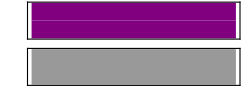

```mathematica
PlaySetChord[{1,2},1.2]
```